## Load Radia

```mathematica
<<Radia`;
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Load Insertion Device Functions

Open and evaluate the notebook “IDFunctions.nb”

## Set Current Working Directory

```mathematica
SetDirectory["C:\\Users\\luana.vilela\\Desktop\\documentacao_onduladores\\Delta22"];
```

## Delta22

## Parameters

```mathematica
(*ID parameters*)
λu = 22; (*Period [mm]*)
Np = 53; (*Number of periods (not including terminations)*)
Br = 1.37; (*Remanent magnetization [T]*)
Gap = 7.5; (*Minimum ID gap [mm]*)
BlockGap = 0;
BlockScale = 1;
BlockVersion = "V3";
Termination = "ThreeBlocksAntiSym"; 

(*Longitudinal range [mm]*)
Lstep = 0.1;
Li = -(Np+2)*λu;
Lf = (Np+2)*λu;
Lnpts =Round[(Lf - Li)/Lstep ]+ 1; 

(*Horizontal range [mm]*)
Hstep =0.1;
Hi = -4;
Hf = 4;
Hnpts = Round[(Hf - Hi)/Hstep ]+ 1; 

(*Particle energy [GeV]*)
Energy = 3;

(*Radia randomization magnitudes*)
radFldLenTol[10^-12,10^-12 ];

(*Radia solver options*)
prec = 0.0000000001;
maxiter = 1000000000;
```

## Model (H/V)

Cassette number of blocks: 219

Cassette number of blocks: 219

Cassette number of blocks: 219

«1 more identical outputs»

IDDelta: elapsed time = 2.001746 s

-Graphics3D-

IDShow: elapsed time = 3.5940545 s

Horizontal field amplitude:    2.43872×10^-8 [T]

Vertical field amplitude:      0.983653 [T]

Longitudinal field amplitude:  3.56163×10^-10 [T]

Horizontal K: 2.02121

Vertical K:   5.01108×10^-8

IDInfo: elapsed time = 1.625157 s

IDPlotFields: elapsed time = 42.0188842 s

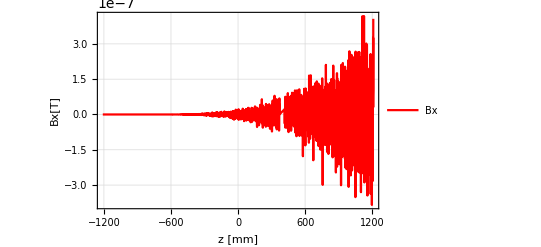
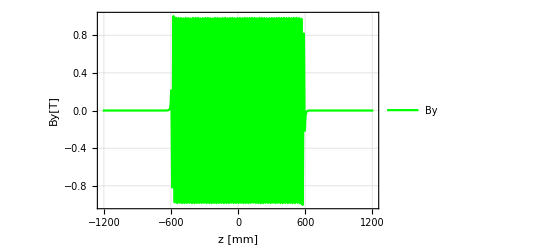
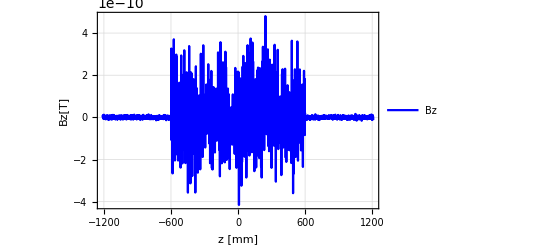

Horizontal field amplitude:    2.66451×10^-8 [T]

Vertical field amplitude:      0.959678 [T]

Longitudinal field amplitude:  2.90525×10^-10 [T]

Horizontal K: 1.97195

Vertical K:   5.47504×10^-8

IDInfo: elapsed time = 1.593895 s

```mathematica
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockGap"-> BlockGap, "BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale, "δP"-> 0];
IDShow[Device];
IDInfo[Device, λu];
Print[IDPlotFields[Device, "z", {Li, Lf}]];

mat = RadMatNdFeB[Br];
radMatApl[Device,mat];
RadSolve[Device,prec, maxiter];
IDInfo[Device, λu];
(*IDFieldMap["Delta22_Fieldmap_H.txt", Device, {Hi, Hf}, {0,0}, {Li, Lf}, Hnpts, 1, Lnpts ]*)
```

## Model (C)

Cassette number of blocks: 219

Cassette number of blocks: 219

Cassette number of blocks: 219

«1 more identical outputs»

IDDelta: elapsed time = 1.953284 s

-Graphics3D-

IDShow: elapsed time = 3.265886 s

Horizontal field amplitude:    0.698629 [T]

Vertical field amplitude:      0.69844 [T]

Longitudinal field amplitude:  3.43235×10^-10 [T]

Horizontal K: 1.43516

Vertical K:   1.43554

IDInfo: elapsed time = 1.5939 s

IDPlotFields: elapsed time = 41.5344743 s

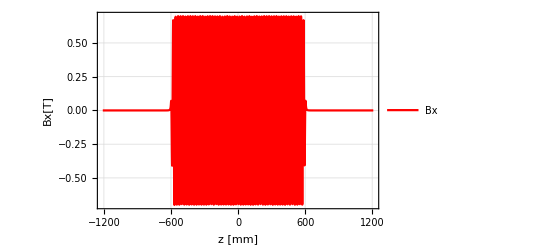
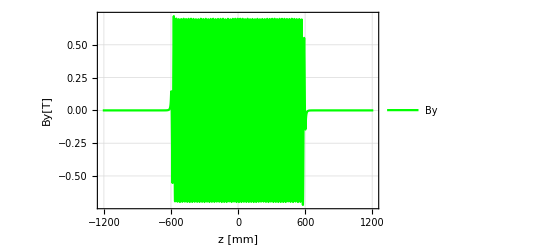
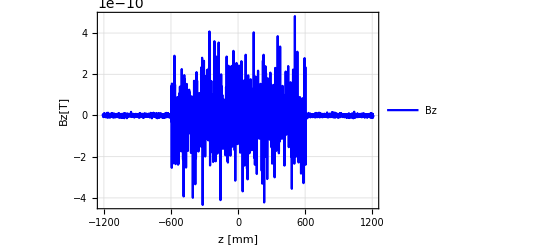

Horizontal field amplitude:    0.680024 [T]

Vertical field amplitude:      0.679843 [T]

Longitudinal field amplitude:  3.08673×10^-10 [T]

Horizontal K: 1.39694

Vertical K:   1.39731

IDInfo: elapsed time = 1.468861 s

```mathematica
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockGap"-> BlockGap, "BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale, "δP"-> λu/4];
IDShow[Device];
IDInfo[Device, λu];
Print[IDPlotFields[Device, "z", {Li, Lf}]];

mat = RadMatNdFeB[Br];
radMatApl[Device,mat];
RadSolve[Device,prec, maxiter];
IDInfo[Device, λu];
(*IDFieldMap["Delta22_Fieldmap_C.txt", Device, {Hi, Hf}, {0,0}, {Li, Lf}, Hnpts, 1, Lnpts ]*)
```

## Integral vs phase

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.296893 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234409 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234379 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234403 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234383 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.218768 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.250022 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.218777 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234381 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234392 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234394 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.218766 s

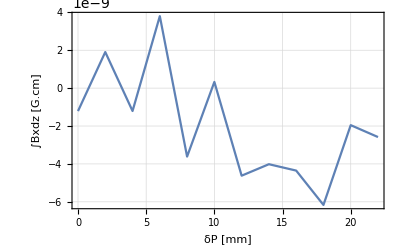

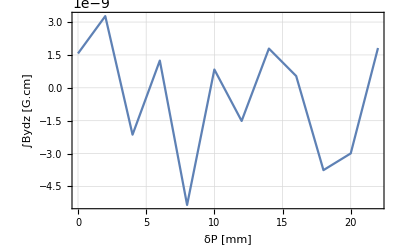

```mathematica
ibx = {};
iby = {};
δPs = Range[0, λu, 2];
For[i=1, i≤ Length[δPs], i++,
δP= δPs[[i]];
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockGap"-> BlockGap, "BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale, "δP"-> δP];
ib = radFldInt[Device,"inf","ibxiby",{0, 0, Li},{0, 0, Lf}]*1000;
AppendTo[ibx, ib[[1]]];
AppendTo[iby, ib[[2]]];
];
ListPlot[Transpose@{δPs, ibx}, Joined->True, PlotTheme->"Detailed", FrameLabel->{"δP [mm]", "∫Bxdz [G.cm]"}]
ListPlot[Transpose@{δPs, iby}, Joined->True, PlotTheme->"Detailed", FrameLabel->{"δP [mm]", "∫Bydz [G.cm]"}]
```

## Integral vs transversal position

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.265673 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.218769 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.234405 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.218758 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.21876 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.250031 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.218758 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.281275 s

Cassette number of blocks: 27

Cassette number of blocks: 27

Cassette number of blocks: 27

«1 more identical outputs»

IDDelta: elapsed time = 0.250021 s

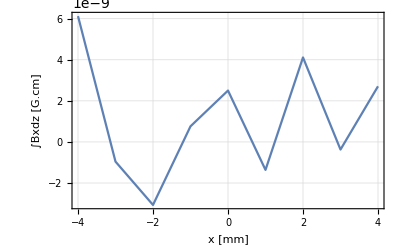

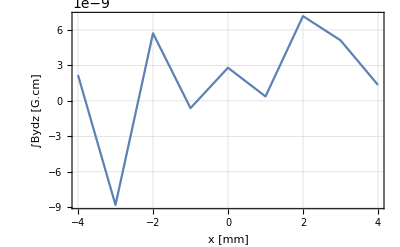

```mathematica
δP = 0;
ibx = {};
iby = {};
xs = Range[Hi, Hf, 1];
For[i=1, i≤ Length[xs], i++,
x= xs[[i]];
Device= IDDelta[λu, Np, Br, Gap,"Termination"->Termination, "BlockGap"-> BlockGap, "BlockVersion"-> BlockVersion, "BlockScale"-> BlockScale, "δP"-> δP];
ib = radFldInt[Device,"inf","ibxiby",{x, 0, Li},{x, 0, Lf}]*1000;
AppendTo[ibx, ib[[1]]];
AppendTo[iby, ib[[2]]];
];
ListPlot[Transpose@{xs, ibx}, Joined->True, PlotTheme->"Detailed", FrameLabel->{"x [mm]", "∫Bxdz [G.cm]"}]
ListPlot[Transpose@{xs, iby}, Joined->True, PlotTheme->"Detailed", FrameLabel->{"x [mm]", "∫Bydz [G.cm]"}]
```